```mathematica
(* Narrowband pulses with fixed profile bandwidths ϵ = 0.9, 0.8, 0.7, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/4 *)
(* Error < 10^-3 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootNB;
err=0.001;
error=", error="<>ToString@err;
totalArea[rule_,npulses_]:=Module[{vars=rule/.Rule[a_,b_]->a},npulses Abs[vars[[-1]]/.rule]];
```

```mathematica
(*N=3 -- None found*)
```

NB4; p=1, error=0.001

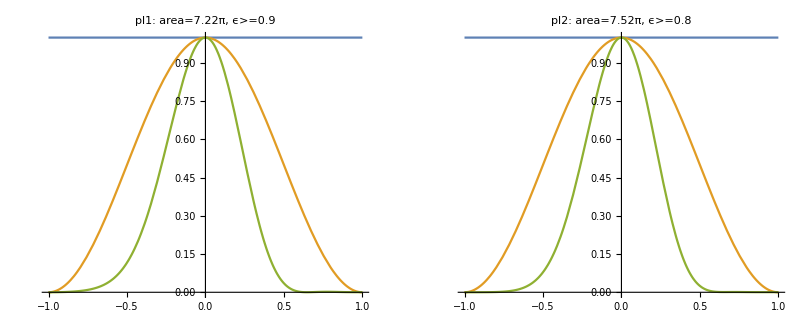

NB4; p=1/2, error=0.001

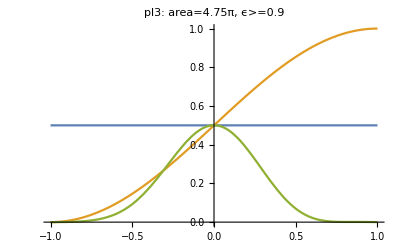

NB4; p=1/4, error=0.001

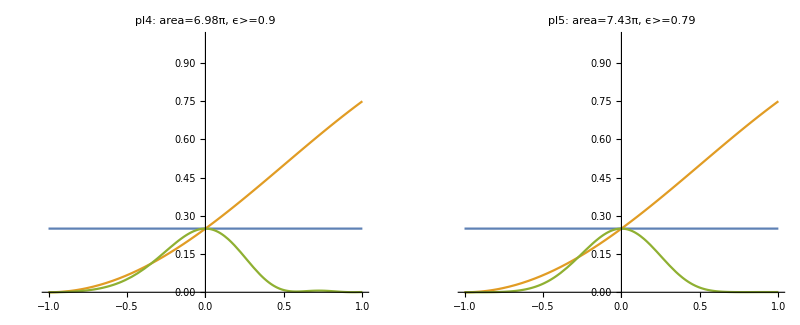

```mathematica
(*N=4 - Huge Area*)
sequence=U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,4]]

pl1=pltN[1.0,{Δ1->2.0012,Δ2->-12.5151,Δ3->2.0929,Δ4->-10.6390,Ω1->1.8059},"pl1"];
pl2=pltN[1.0,{Δ1->-12.3379,Δ2->1.9371,Δ3->-14.5486,Δ4->2.0388,Ω1->1.8805},"pl2"];

pl3=pltN[0.5,{Δ1->0.3484,Δ2->-22.967,Δ3->7.6217,Δ4->0.4113,Ω1->1.1871},"pl3"];

pl4=pltN[0.25,{Δ1->10.1440,Δ2->5.6478,Δ3->2.3187,Δ4->8.3743,Ω1->1.7444},"pl4"];
pl5=pltN[0.25,{Δ1->6.5307,Δ2->-32.0600,Δ3->1.8512,Δ4->8.3877,Ω1->1.8580},"pl5"];

GGrid[Text[Style["NB4; p=1"<> error,FontSize->20]],{{pl1,pl2,Null,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/2"<> error,FontSize->20]],{{pl3,Null,Null,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/4"<> error,FontSize->20]],{{pl4,pl5,Null,Null,Null}},ImageSize->Full]
```

NB5; p=1, error=0.001

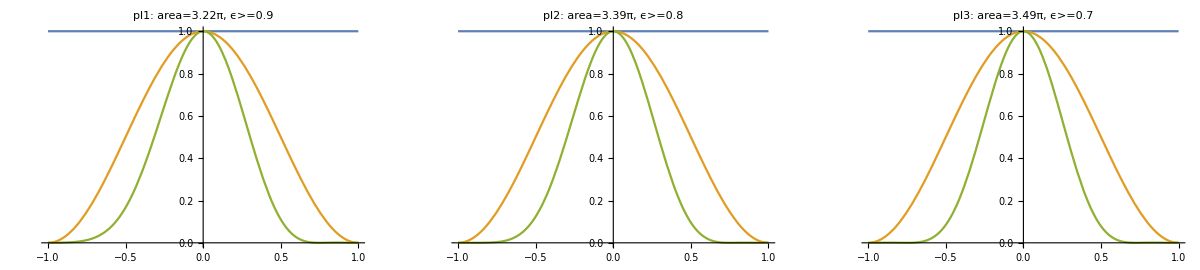

NB5; p=1/2, error=0.001

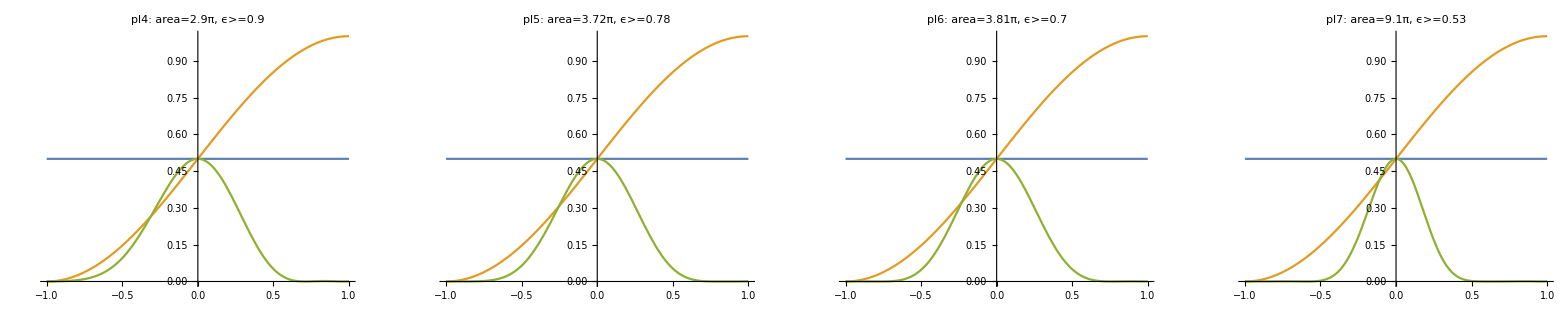

NB5; p=1/4, error=0.001

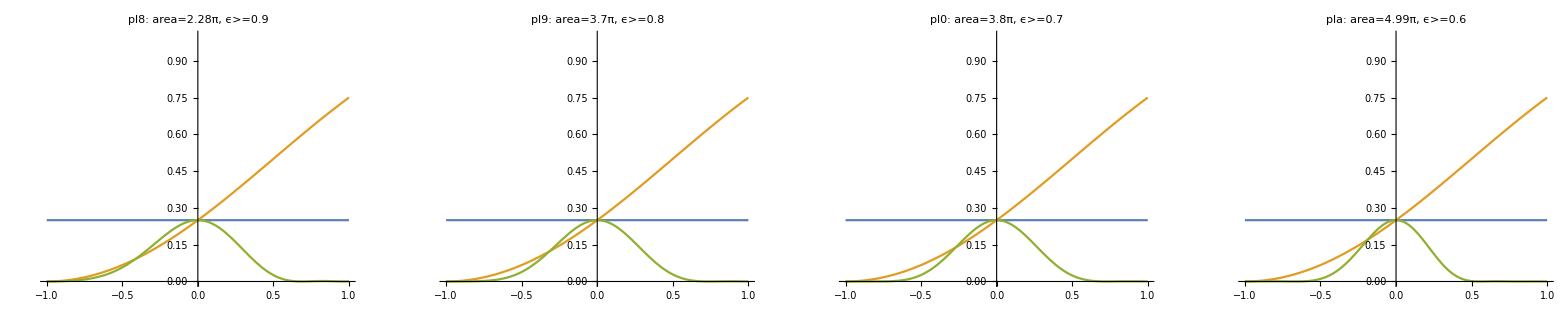

```mathematica
(*N=5*)
sequence=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,5]]

pl1=plt[1.0,{Δ1->0.0847,Δ2->-0.9787,Δ3->4.4441,Ω1->0.6433},"pl1"];
pl2=plt[1.0,{Δ1->0.0801,Δ2->-1.0220,Δ3->6.6014,Ω1->0.6782},"pl2"];
pl3=plt[1.0,{Δ1->0.0755,Δ2->-1.0027,Δ3->6.6328,Ω1->0.6971},"pl3"];

pl4=plt[0.5,{Δ1->0.2114,Δ2->0.1058,Δ3->4.8119,Ω1->0.5799},"pl4"];
pl5=plt[0.5,{Δ1->0.4212,Δ2->-1.4086,Δ3->27.1464,Ω1->0.7435},"pl5"];
pl6=plt[0.5,{Δ1->0.4305,Δ2->-1.3691,Δ3->13.0894,Ω1->0.7620},"pl6"];
pl7=plt[0.5,{Δ1->6.2772,Δ2->-1.7160,Δ3->6.5815,Ω1->1.8201},"pl7"];

pl8=plt[0.25,{Δ1->0.2837,Δ2->-0.1887,Δ3->1.2858,Ω1->0.4563},"pl8"];
pl9=plt[0.25,{Δ1->0.6007,Δ2->-1.5393,Δ3->9.2371,Ω1->0.7391},"pl9"];
pl0=plt[0.25,{Δ1->0.5976,Δ2->-1.4907,Δ3->9.1770,Ω1->0.7591},"pl0"];
pla=plt[0.25,{Δ1->-2.5915,Δ2->-0.567,Δ3->3.7832,Ω1->0.9987},"pla"];

GGrid[Text[Style["NB5; p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,Null}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/2"<> error,FontSize->20]],{{pl4,pl5,pl6,pl7}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/4"<> error,FontSize->20]],{{pl8,pl9,pl0,pla}},ImageSize->Full]
```

NB6; p=1, error=0.001

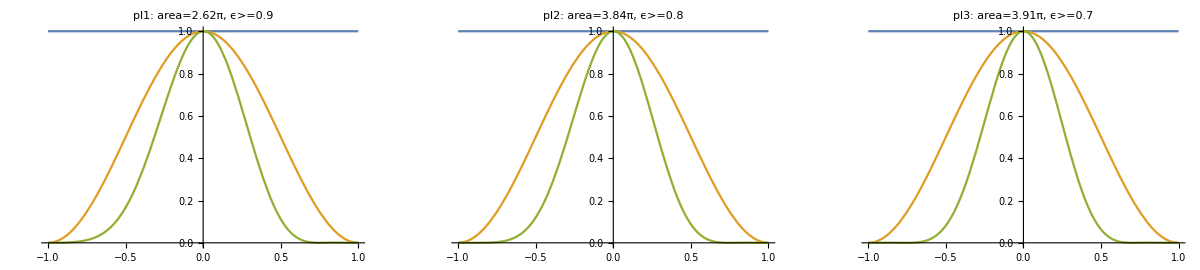

NB6; p=1/2, error=0.001

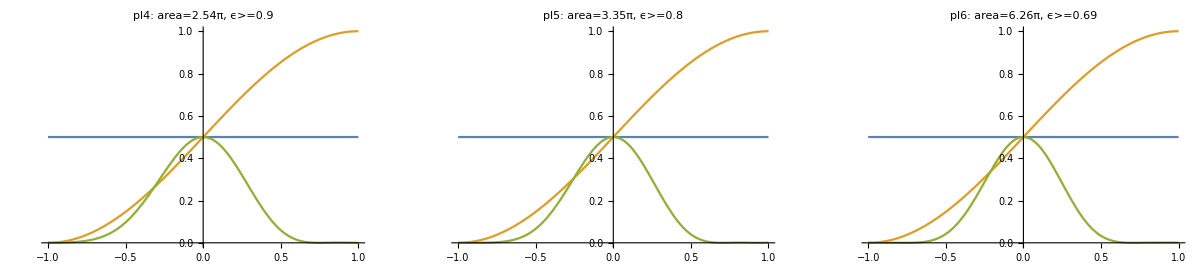

NB6; p=1/4, error=0.001

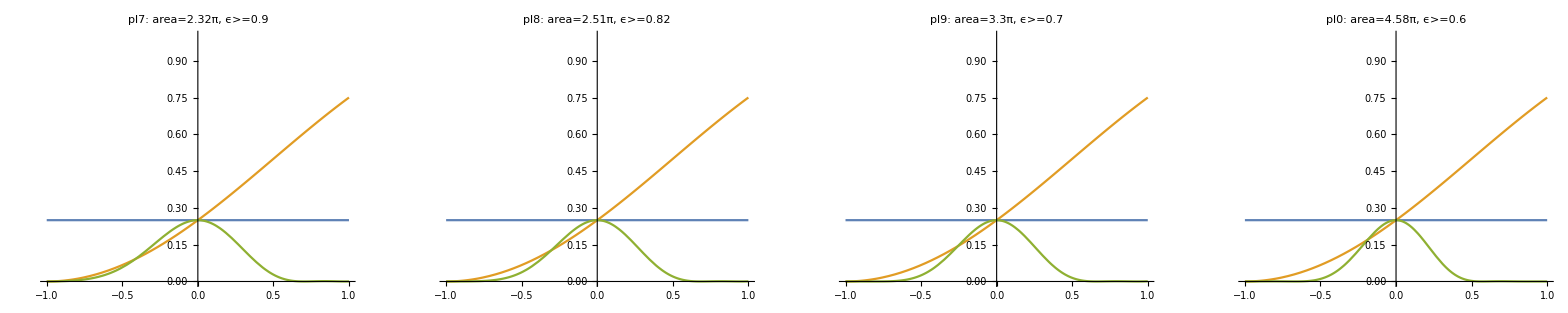

```mathematica
(*N=6 - many of NB4 with Unequal Rabi have smaller total area*)
sequence=U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,6]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,0,label, totalArea[rule,6]]

pl1=pltS[1.0,{Δ1->-0.4929,Δ2->0.5626,Δ3->0.3872,Ω1->0.4366},"pl1"];
pl2=pltS[1.0,{Δ1->0.6601,Δ2->-2.3117,Δ3->0.6574,Ω1->0.6395},"pl2"];
pl3=pltS[1.0,{Δ1->0.6364,Δ2->-2.2958,Δ3->0.6205,Ω1->0.6522},"pl3"];

pl4=pltS[0.5,{Δ1->-0.405,Δ2->0.8379,Δ3->0.2192,Ω1->0.423},"pl4"];
pl5=pltS[0.5,{Δ1->-0.2162,Δ2->2.5968,Δ3->0.3189,Ω1->0.5589},"pl5"];
pl6=pltS[0.5,{Δ1->1.0411,Δ2->-8.5422,Δ3->3.5607,Ω1->1.0434},"pl6"];

pl7=pltS[0.25,{Δ1->-0.6316,Δ2->0.1448,Δ3->0.6669,Ω1->0.3862},"pl7"];
pl8=pltS[0.25,{Δ1->-0.3436,Δ2->0.92,Δ3->0.1224,Ω1->0.4191},"pl8"];
pl9=pltS[0.25,{Δ1->-0.1684,Δ2->2.6905,Δ3->0.2204,Ω1->0.5497},"pl9"];
pl0=pltS[0.25,{Δ1->2.6133,Δ2->0.735,Δ3->1.031,Ω1->0.7626},"pl0"];

GGrid[Text[Style["NB6; p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,Null}},ImageSize->Full]
GGrid[Text[Style["NB6; p=1/2"<> error,FontSize->20]],{{pl4,pl5,pl6,Null}},ImageSize->Full]
GGrid[Text[Style["NB6; p=1/4"<> error,FontSize->20]],{{pl7,pl8,pl9,pl0}},ImageSize->Full]
```

NB7; p=1, error=0.001

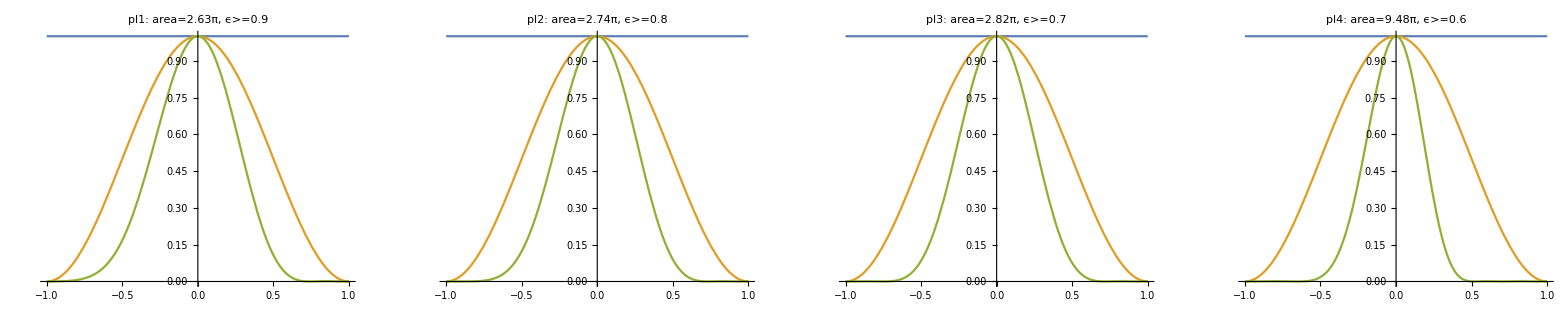

NB7; p=1/2, error=0.001

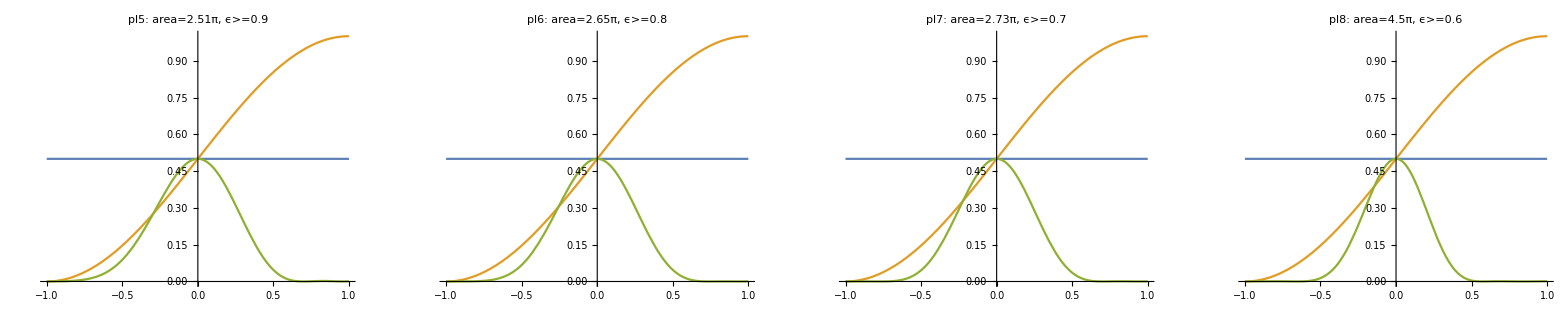

NB7; p=1/4, error=0.001

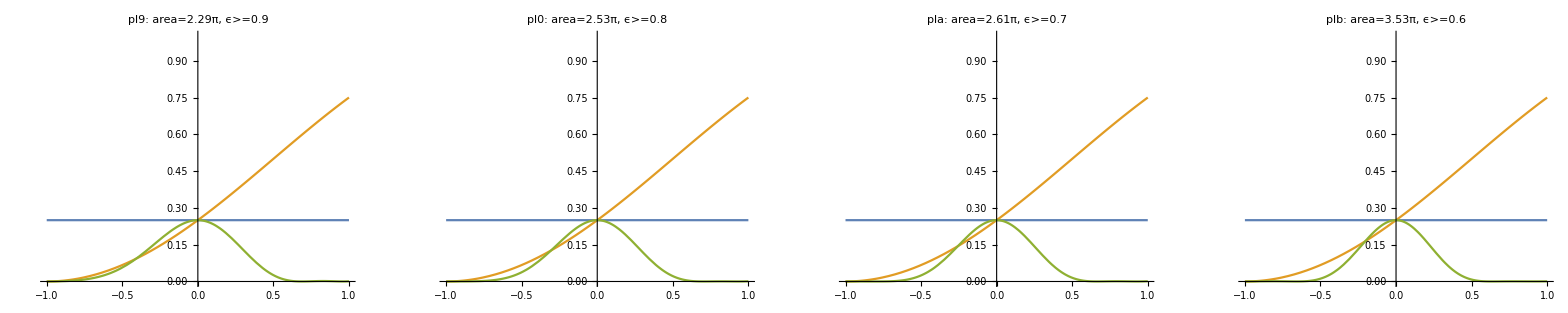

```mathematica
(*N=7 - Chooose this*)
sequence=U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label,totalArea[rule,7]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,0,label, totalArea[rule,7]]

pl1=pltS[1.0,{Δ1->0.1837,Δ2->0.353,Δ3->-0.1335,Δ4->0.9579,Ω1->0.3759},"pl1"];
pl2=pltS[1.0,{Δ1->0.0612,Δ2->-0.0468,Δ3->-0.795,Δ4->0.2863,Ω1->0.3908},"pl2"];
pl3=pltS[1.0,{Δ1->0.679,Δ2->-0.112,Δ3->0.2548,Δ4->0.5527,Ω1->0.4029},"pl3"];
pl4=pltS[1.0,{Δ1->6.6763,Δ2->-2.2795,Δ3->-1.6077,Δ4->6.5281,Ω1->-1.3548},"pl4"];

pl5=pltS[0.5,{Δ1->-0.2161,Δ2->-0.1899,Δ3->0.7714,Δ4->0.1395,Ω1->0.3584},"pl5"];
pl6=pltS[0.5,{Δ1->-0.0126,Δ2->0.2751,Δ3->-0.2186,Δ4->1.1631,Ω1->0.3788},"pl6"];
pl7=pltS[0.5,{Δ1->-0.018,Δ2->0.2736,Δ3->-0.2289,Δ4->1.1464,Ω1->-0.3893},"pl7"];
pl8=pltS[0.5,{Δ1->0.399,Δ2->0.7979,Δ3->0.7077,Δ4->-2.8359,Ω1->-0.6429},"pl8"];

pl9=pltS[0.25,{Δ1->0.4024,Δ2->0.1692,Δ3->-0.6148,Δ4->-0.4619,Ω1->0.327},"pl9"];
pl0=pltS[0.25,{Δ1->0.8149,Δ2->0.1541,Δ3->0.3442,Δ4->0.3433,Ω1->0.3615},"pl0"];
pla=pltS[0.25,{Δ1->-0.0621,Δ2->0.2358,Δ3->-0.2386,Δ4->1.2227,Ω1->0.3731},"pla"];
plb=pltS[0.25,{Δ1->0.5541,Δ2->-0.4118,Δ3->0.575,Δ4->-1.7846,Ω1->0.5037},"plb"];

GGrid[Text[Style["NB7; p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
GGrid[Text[Style["NB7; p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8}},ImageSize->Full]
GGrid[Text[Style["NB7; p=1/4"<> error,FontSize->20]],{{pl9,pl0,pla,plb}},ImageSize->Full]
```